```mathematica
Table[FullVector[k],{k,Select[Keys[allGraphs],VertexCount[allGraphs[#,"graph"]]==4&]}]//Sort//Length
```

64

```mathematica
Table[FullVector[k],{k,Select[Keys[allGraphs],VertexCount[allGraphs[#,"graph"]]==4&]}]
```

```mathematica
fullSymbols5=Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],CompareSymbols]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x34x5,v1x2x35x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x45,v1x24x35,v1x25x34,v12x3x45,v12x34x5,v12x35x4,v13x2x45,v13x24x5,v13x25x4,v14x2x35,v14x23x5,v14x25x3,v15x2x34,v15x23x4,v15x24x3,v1x2x345,v1x234x5,v1x235x4,v1x245x3,v123x4x5,v124x3x5,v125x3x4,v134x2x5,v135x2x4,v145x2x3,v12x345,v123x45,v124x35,v125x34,v13x245,v134x25,v135x24,v14x235,v145x23,v15x234,v1x2345,v1234x5,v1235x4,v1245x3,v1345x2,v12345}

```mathematica
FullVector5[k_]:=Table[Coefficient[allGraphs5[k,"colofour"],s],{s,fullSymbols5}]
```

```mathematica
Map[PadLeft[IntegerDigits[#,2],52]&,Sort[Table[FromDigits[FullVector5[k],2],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]]]//Total
```

{1024,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,128,128,128,128,128,128,128,128,128,128,64,64,64,64,64,64,64,64,64,64,16,16,16,16,16,1}

## Two nodes

```mathematica
fullSymbols2=Sort[Table[allGraphs2[k,"colofour"],{k,allGraphs2AtomKeys}],CompareSymbols]
```

{v1x2,v12}

```mathematica
FullVector2[k_]:=Table[Coefficient[allGraphs2[k,"colofour"],s],{s,fullSymbols2}]
```

```mathematica
Map[PadLeft[IntegerDigits[#,2],BellB[2]]&,Sort[Table[FromDigits[FullVector2[k],2],{k,Select[Keys[allGraphs2],VertexCount[allGraphs2[#,"graph"]]==2&]}]]]//Total
```

{2,1}

```mathematica
TableForm[Map[PadLeft[IntegerDigits[#,2],BellB[2]]&,Sort[Table[FromDigits[FullVector2[k],2],{k,Select[Keys[allGraphs2],VertexCount[allGraphs2[#,"graph"]]==2&]}]]],TableSpacing->{0, 0}]
```

1 | 0
1 | 1

## Three nodes

```mathematica
fullSymbols3=Sort[Table[allGraphs3[k,"colofour"],{k,allGraphs3AtomKeys}],CompareSymbols]
```

{v1x2x3,v1x23,v12x3,v13x2,v123}

```mathematica
FullVector3[k_]:=Table[Coefficient[allGraphs3[k,"colofour"],s],{s,fullSymbols3}]
```

```mathematica
Map[PadLeft[IntegerDigits[#,2],BellB[3]]&,Sort[Table[FromDigits[FullVector3[k],2],{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&]}]]]//Total
```

{8,4,4,4,1}

```mathematica
TableForm[Map[colorify[PadLeft[IntegerDigits[#,2],BellB[3]],3]&,Sort[Table[FromDigits[FullVector3[k],2],{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&]}]]],TableSpacing->{0, 0}]
```

1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1

## Four nodes

```mathematica
fullSymbols4=Sort[Table[allGraphs4[k,"colofour"],{k,allGraphs4AtomKeys}],CompareSymbols]
```

{v1x2x3x4,v1x2x34,v1x23x4,v1x24x3,v12x3x4,v13x2x4,v14x2x3,v12x34,v13x24,v14x23,v1x234,v123x4,v124x3,v134x2,v1234}

```mathematica
FullVector4[k_]:=Table[Coefficient[allGraphs4[k,"colofour"],s],{s,fullSymbols4}]
```

```mathematica
Map[PadLeft[IntegerDigits[#,2],BellB[4]]&,Sort[Table[FromDigits[FullVector4[k],2],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]]]//Total
```

{64,32,32,32,32,32,32,16,16,16,8,8,8,8,1}

```mathematica
Zones=Accumulate[Table[StirlingS2[4,k],{k,1,4}]]
```

{1,8,14,15}

```mathematica
colorify[vector_,nodes_]:=Block[{i,colors={Darker[Green],Black}, color =1,zonePos=1,result=vector,Zones=Accumulate[Table[StirlingS2[nodes,k],{k,1,nodes}]]},
For[i=1,i≤BellB[nodes],i++,
result[[i]]=Style[result[[i]],colors[[color]]];
If[i==Zones[[zonePos]],
If[color==1, color = 2, color=1];
zonePos++;
]
];
result
]
```

```mathematica
Drop[Range[15],{2,8}]
```

{1,9,10,11,12,13,14,15}

```mathematica
TableForm[DeleteDuplicates[Map[colorify[PadLeft[IntegerDigits[#,2],BellB[4]-StirlingS2[4,2]],3]&,Sort[Table[FromDigits[Drop[FullVector4[k],{2,8}],2],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]]]],TableSpacing->{0, 0}]
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

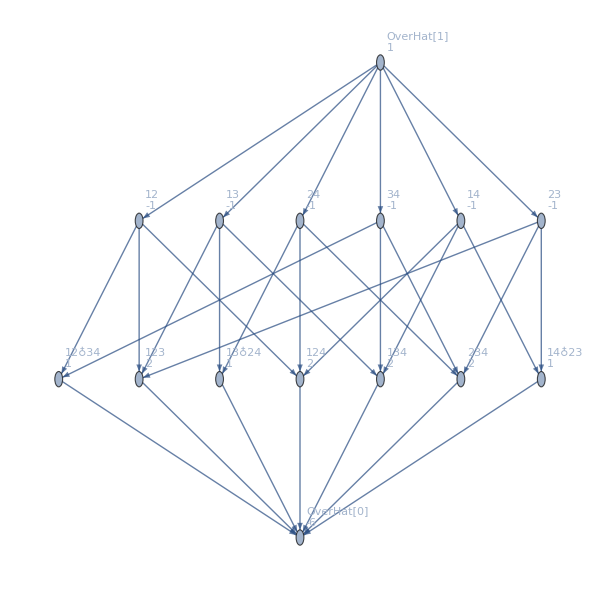

```mathematica
MobiusGraph5[K4Key,allGraphs4]
```

```mathematica
fullSymbols4/.{v1x2x3x4-
```

{v1x2x3x4,v1x2x34,v1x23x4,v1x24x3,v12x3x4,v13x2x4,v14x2x3,v12x34,v13x24,v14x23,v1x234,v123x4,v124x3,v134x2,v1234}

```mathematica
TableForm[Map[colorify[PadLeft[IntegerDigits[#,2],BellB[4]],4]&,Sort[Table[FromDigits[FullVector4[k],2],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]]],TableSpacing->{0, 0}]
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

```mathematica
Map[PadLeft[IntegerDigits[#,2],BellB[4]]&,Sort[Table[FromDigits[FullVector4[k],2],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==3&]}]]]//Total
```

{0,8,8,8,8,8,8,8,8,8,12,12,12,12,6}

```mathematica
TableForm[Map[PadLeft[IntegerDigits[#,2],BellB[4]]&,Sort[Table[FromDigits[FullVector4[k],2],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==3&]}]]],TableSpacing->{0, 0}]
```

0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1

## Five nodes

```mathematica
fullSymbols5=Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],CompareSymbols]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x34x5,v1x2x35x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x45,v1x24x35,v1x25x34,v12x3x45,v12x34x5,v12x35x4,v13x2x45,v13x24x5,v13x25x4,v14x2x35,v14x23x5,v14x25x3,v15x2x34,v15x23x4,v15x24x3,v1x2x345,v1x234x5,v1x235x4,v1x245x3,v123x4x5,v124x3x5,v125x3x4,v134x2x5,v135x2x4,v145x2x3,v12x345,v123x45,v124x35,v125x34,v13x245,v134x25,v135x24,v14x235,v145x23,v15x234,v1x2345,v1234x5,v1235x4,v1245x3,v1345x2,v12345}

```mathematica
fullnull5=Map[Symbol["n"<>StringDrop[SymbolName[#],1]]&,fullSymbols5]
```

{n1x2x3x4x5,n1x2x3x45,n1x2x34x5,n1x2x35x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x45,n1x24x35,n1x25x34,n12x3x45,n12x34x5,n12x35x4,n13x2x45,n13x24x5,n13x25x4,n14x2x35,n14x23x5,n14x25x3,n15x2x34,n15x23x4,n15x24x3,n1x2x345,n1x234x5,n1x235x4,n1x245x3,n123x4x5,n124x3x5,n125x3x4,n134x2x5,n135x2x4,n145x2x3,n12x345,n123x45,n124x35,n125x34,n13x245,n134x25,n135x24,n14x235,n145x23,n15x234,n1x2345,n1234x5,n1235x4,n1245x3,n1345x2,n12345}

```mathematica
FullVector5[k_]:=Table[Coefficient[allGraphs5[k,"colofour"],s],{s,fullSymbols5}]
```

```mathematica
Map[PadLeft[IntegerDigits[#,2],BellB[5]]&,Sort[Table[FromDigits[FullVector5[k],2],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]]]//Total
```

{1024,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,128,128,128,128,128,128,128,128,128,128,64,64,64,64,64,64,64,64,64,64,16,16,16,16,16,1}

```mathematica
Zones=Accumulate[Table[StirlingS2[5,k],{k,1,5}]]
```

{1,16,41,51,52}

```mathematica
colorify[vector_,nodes_]:=Block[{i,colors={Darker[Green],Black}, color =1,zonePos=1,result=vector,Zones=Accumulate[Table[StirlingS2[nodes,k],{k,1,nodes}]]},
For[i=1,i≤BellB[nodes],i++,
result[[i]]=Style[result[[i]],colors[[color]]];
If[i==Zones[[zonePos]],
If[color==1, color = 2, color=1];
zonePos++;
]
];
result
]
```

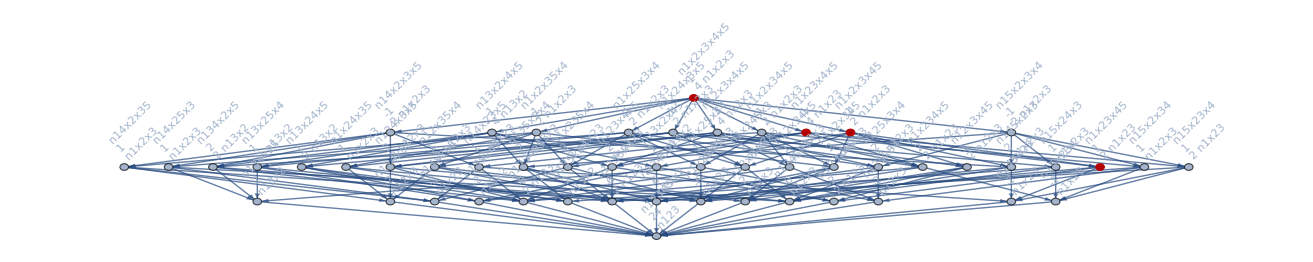

```mathematica
g=Graph[MobiusGraph4[K5Key,allGraphs5],GraphHighlight->{n1x23x45,n1x23x4x5,n1x2x3x45,n1x2x3x4x5}]
```

```mathematica
five3=Select[fullnull5,StringCount[SymbolName[#],"x"]==2&]
```

{n1x23x45,n1x24x35,n1x25x34,n12x3x45,n12x34x5,n12x35x4,n13x2x45,n13x24x5,n13x25x4,n14x2x35,n14x23x5,n14x25x3,n15x2x34,n15x23x4,n15x24x3,n1x2x345,n1x234x5,n1x235x4,n1x245x3,n123x4x5,n124x3x5,n125x3x4,n134x2x5,n135x2x4,n145x2x3}

```mathematica
VertexList[g]
```

{n12x34x5,n12x35x4,n12x3x45,n13x24x5,n13x25x4,n13x2x45,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x23x45,n1x24x35,n1x25x34,n1x2x3x4x5,n12345,n1234x5,n1235x4,n123x45,n123x4x5,n1245x3,n124x35,n124x3x5,n125x34,n125x3x4,n12x345,n12x3x4x5,n1345x2,n134x25,n134x2x5,n135x24,n135x2x4,n13x245,n13x2x4x5,n145x23,n145x2x3,n14x235,n14x2x3x5,n15x234,n15x2x3x4,n1x2345,n1x234x5,n1x235x4,n1x23x4x5,n1x245x3,n1x24x3x5,n1x25x3x4,n1x2x345,n1x2x34x5,n1x2x35x4,n1x2x3x45}

```mathematica
Table[VertexInComponent[g,v],{v,five3}]
```

{{n1x23x45,n1x23x4x5,n1x2x3x45,n1x2x3x4x5},{n1x24x35,n1x24x3x5,n1x2x35x4,n1x2x3x4x5},{n1x25x34,n1x25x3x4,n1x2x34x5,n1x2x3x4x5},{n12x3x45,n12x3x4x5,n1x2x3x45,n1x2x3x4x5},{n12x34x5,n12x3x4x5,n1x2x34x5,n1x2x3x4x5},{n12x35x4,n12x3x4x5,n1x2x35x4,n1x2x3x4x5},{n13x2x45,n13x2x4x5,n1x2x3x45,n1x2x3x4x5},{n13x24x5,n13x2x4x5,n1x24x3x5,n1x2x3x4x5},{n13x25x4,n13x2x4x5,n1x25x3x4,n1x2x3x4x5},{n14x2x35,n14x2x3x5,n1x2x35x4,n1x2x3x4x5},{n14x23x5,n14x2x3x5,n1x23x4x5,n1x2x3x4x5},{n14x25x3,n14x2x3x5,n1x25x3x4,n1x2x3x4x5},{n15x2x34,n15x2x3x4,n1x2x34x5,n1x2x3x4x5},{n15x23x4,n15x2x3x4,n1x23x4x5,n1x2x3x4x5},{n15x24x3,n15x2x3x4,n1x24x3x5,n1x2x3x4x5},{n1x2x345,n1x2x34x5,n1x2x35x4,n1x2x3x45,n1x2x3x4x5},{n1x234x5,n1x23x4x5,n1x24x3x5,n1x2x34x5,n1x2x3x4x5},{n1x235x4,n1x23x4x5,n1x25x3x4,n1x2x35x4,n1x2x3x4x5},{n1x245x3,n1x24x3x5,n1x25x3x4,n1x2x3x45,n1x2x3x4x5},{n123x4x5,n12x3x4x5,n13x2x4x5,n1x23x4x5,n1x2x3x4x5},{n124x3x5,n12x3x4x5,n14x2x3x5,n1x24x3x5,n1x2x3x4x5},{n125x3x4,n12x3x4x5,n15x2x3x4,n1x25x3x4,n1x2x3x4x5},{n134x2x5,n13x2x4x5,n14x2x3x5,n1x2x34x5,n1x2x3x4x5},{n135x2x4,n13x2x4x5,n15x2x3x4,n1x2x35x4,n1x2x3x4x5},{n145x2x3,n14x2x3x5,n15x2x3x4,n1x2x3x45,n1x2x3x4x5}}

```mathematica
Table[If[MemberQ[{n1x23x4x5,n1x2x3x45,n1x2x3x4x5},s],1,0],{s,fullnull5}]
```

{1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Select[Keys[allGraphs5],FullVector5[#]=={1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}&]
```

{}